```mathematica
ad=({{0, 0}, {1, 0}});
a=({{0, 1}, {0, 0}});
bd=({{0, 0}, {1, 0}});
b=({{0, 1}, {0, 0}});
i=({{1, 0}, {0, 1}});
```

{0.996923,{t→1.74264}}

0.996923

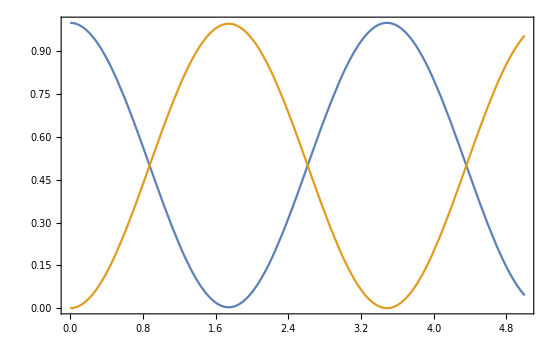

```mathematica
ωa=7;
ωb=7.1;
g=0.9;
ada=KroneckerProduct[ad.a,i];
bdb=KroneckerProduct[i,bd.b];
adb=KroneckerProduct[ad,b];
abd=KroneckerProduct[a,bd];
H=Simplify[ωa *ada+ωb* bdb + g*(adb+abd)];
Eigensystem[H];
e2=Eigensystem[H][[1,2]];
e3=Eigensystem[H][[1,3]];
v2=Eigensystem[H][[2,2]];
v3=Eigensystem[H][[2,3]];
v0=Simplify[((-v3[[2]])/(v3[[3]]v2[[2]]-v3[[2]]v2[[3]])v2+v2[[2]]/(v3[[3]]v2[[2]]-v3[[2]]v2[[3]])v3)];
vt[t_]:={Simplify[(-v3[[2]])/(v3[[3]]v2[[2]]-v3[[2]]v2[[3]])v2 E^(-I e2 t)+v2[[2]]/(v3[[3]]v2[[2]]-v3[[2]]v2[[3]])v3 E^(-I e3 t)]}ᵀ
ExpB[t_]:=FullSimplify[vt[t]† .bdb.vt[t],Assumptions->{t>0}]
ExpA[t_]:=Simplify[vt[t]† .ada.vt[t]]
FindMaximum[Re[ExpB[t][[1]]],{t,0.1,50}]
1-(ωa-ωb)^2/(4 g^2+(ωa-ωb)^2)
Plot[{ExpA[t],ExpB[t]},{t,0,5},Frame->True,PlotRange->{{0,5},{0,1}}]
```